```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
datadir="/home/cal422/PycharmProjects/Hyperbolic_Lattice_Self_Consistent_Hartree_Fock_Data_Acquisition/Mathematica_Final_Plots/Final_Data/NH_withBField_FinalHoneycombScalingData/Eigenvalue_Data";
```

```mathematica
a0b0d05ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.05__eigvals.txt"],"Data"]]][[1]];
a0b0d1ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.1__eigvals.txt"],"Data"]]][[1]];
a0b0d15ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.15__eigvals.txt"],"Data"]]][[1]];
a0b0d2ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.2__eigvals.txt"],"Data"]]][[1]];
a0b0d25ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.25__eigvals.txt"],"Data"]]][[1]];
a0b0d3ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.3__eigvals.txt"],"Data"]]][[1]];
a0b0d35ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.35__eigvals.txt"],"Data"]]][[1]];
a0b0d4ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0_b0.4__eigvals.txt"],"Data"]]][[1]];
```

```mathematica
a0d2b0d05ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.05__eigvals.txt"],"Data"]]][[1]];
a0d2b0d1ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.1__eigvals.txt"],"Data"]]][[1]];
a0d2b0d15ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.15__eigvals.txt"],"Data"]]][[1]];
a0d2b0d2ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.2__eigvals.txt"],"Data"]]][[1]];
a0d2b0d25ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.25__eigvals.txt"],"Data"]]][[1]];
a0d2b0d3ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.3__eigvals.txt"],"Data"]]][[1]];
a0d2b0d35ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.35__eigvals.txt"],"Data"]]][[1]];
a0d2b0d4ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.2_b0.4__eigvals.txt"],"Data"]]][[1]];
```

```mathematica
a0d4b0d05ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.05__eigvals.txt"],"Data"]]][[1]];
a0d4b0d1ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.1__eigvals.txt"],"Data"]]][[1]];
a0d4b0d15ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.15__eigvals.txt"],"Data"]]][[1]];
a0d4b0d2ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.2__eigvals.txt"],"Data"]]][[1]];
a0d4b0d25ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.25__eigvals.txt"],"Data"]]][[1]];
a0d4b0d3ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.3__eigvals.txt"],"Data"]]][[1]];
a0d4b0d35ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.35__eigvals.txt"],"Data"]]][[1]];
a0d4b0d4ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.4_b0.4__eigvals.txt"],"Data"]]][[1]];
```

```mathematica
a0d6b0d05ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.05__eigvals.txt"],"Data"]]][[1]];
a0d6b0d1ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.1__eigvals.txt"],"Data"]]][[1]];
a0d6b0d15ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.15__eigvals.txt"],"Data"]]][[1]];
a0d6b0d2ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.2__eigvals.txt"],"Data"]]][[1]];
a0d6b0d25ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.25__eigvals.txt"],"Data"]]][[1]];
a0d6b0d3ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.3__eigvals.txt"],"Data"]]][[1]];
a0d6b0d35ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.35__eigvals.txt"],"Data"]]][[1]];
a0d6b0d4ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.6_b0.4__eigvals.txt"],"Data"]]][[1]];
```

```mathematica
a0d8b0d05ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.05__eigvals.txt"],"Data"]]][[1]];
a0d8b0d1ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.1__eigvals.txt"],"Data"]]][[1]];
a0d8b0d15ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.15__eigvals.txt"],"Data"]]][[1]];
a0d8b0d2ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.2__eigvals.txt"],"Data"]]][[1]];
a0d8b0d25ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.25__eigvals.txt"],"Data"]]][[1]];
a0d8b0d3ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.3__eigvals.txt"],"Data"]]][[1]];
a0d8b0d35ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.35__eigvals.txt"],"Data"]]][[1]];
a0d8b0d4ev=Re[Map[cstn,Transpose@Import[StringJoin[datadir,"/honeycomb_nl20a0.8_b0.4__eigvals.txt"],"Data"]]][[1]];
```

### a0 fits

```mathematica
a0e1fits={};
```

```mathematica
bw=(3-(-3))/141;
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{8.99999,{x→0.297872}}

0.297872

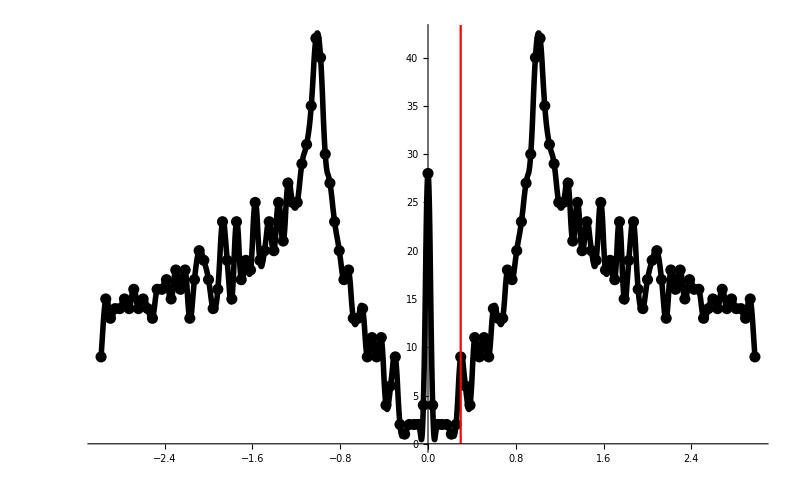

```mathematica
binedges=HistogramList[a0b0d05ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d05ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.4},{x,0.3}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{22.9998,{x→0.425529}}

0.425529

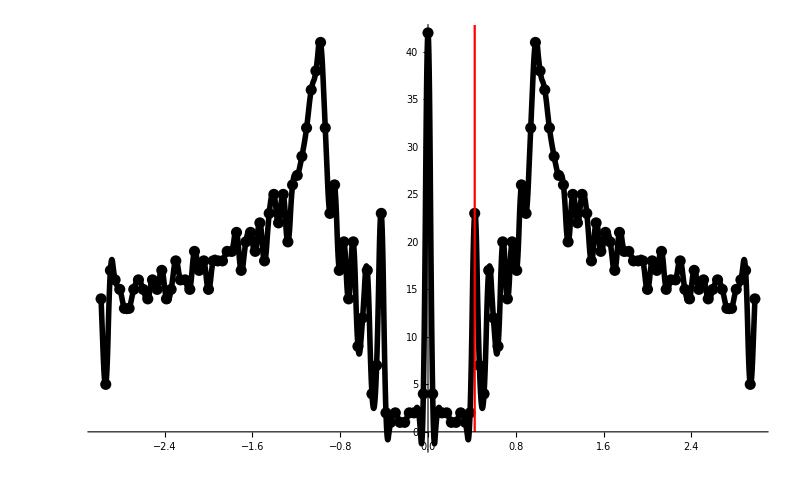

```mathematica
binedges=HistogramList[a0b0d1ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d1ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.3≤x≤0.6},{x,0.45}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{38.9999,{x→0.510636}}

0.510636

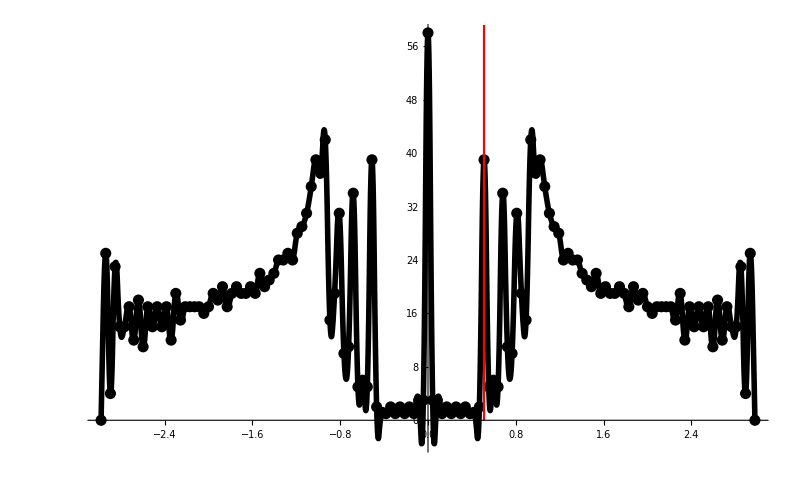

```mathematica
binedges=HistogramList[a0b0d15ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d15ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.6},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{42.9996,{x→0.553189}}

0.553189

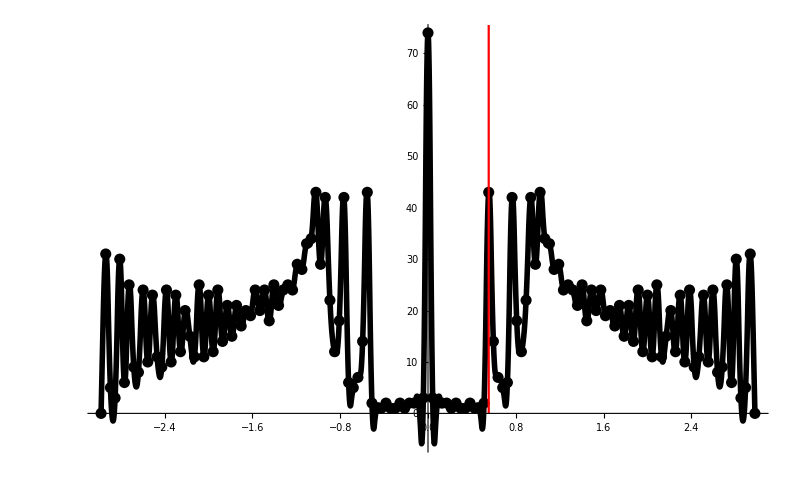

```mathematica
binedges=HistogramList[a0b0d2ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d2ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.6},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{67.9975,{x→0.638272}}

0.638272

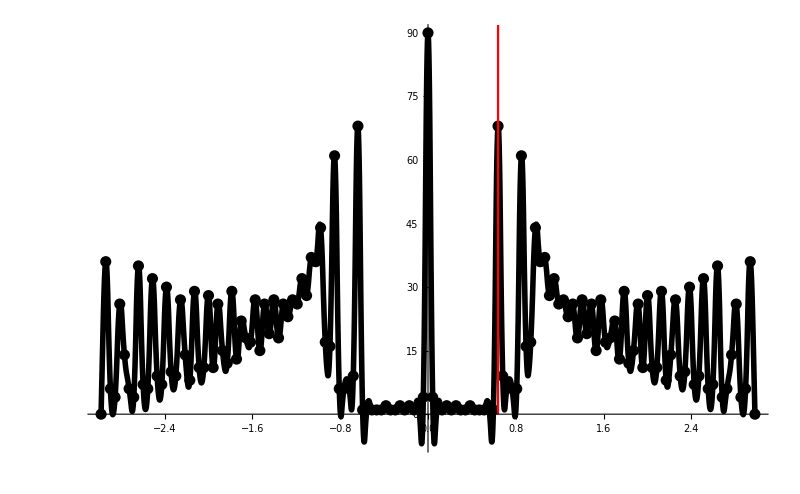

```mathematica
binedges=HistogramList[a0b0d25ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d25ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.8},{x,0.6}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{78.9994,{x→0.680846}}

0.680846

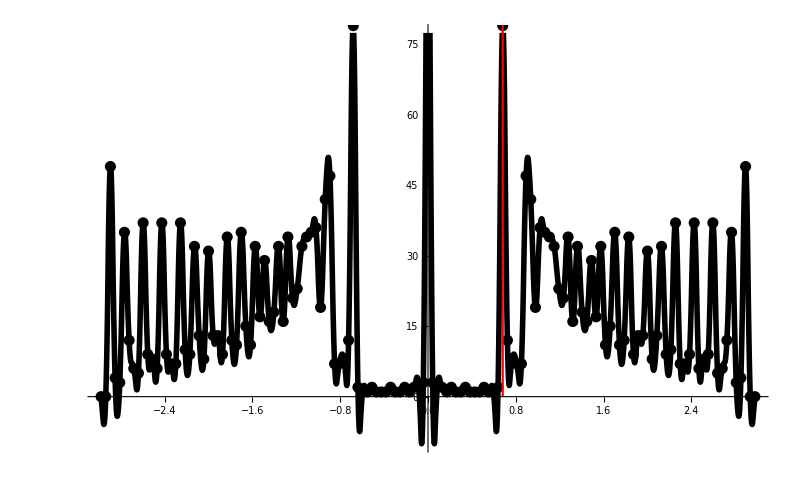

```mathematica
binedges=HistogramList[a0b0d3ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d3ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.8},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{89.9993,{x→0.723401}}

0.723401

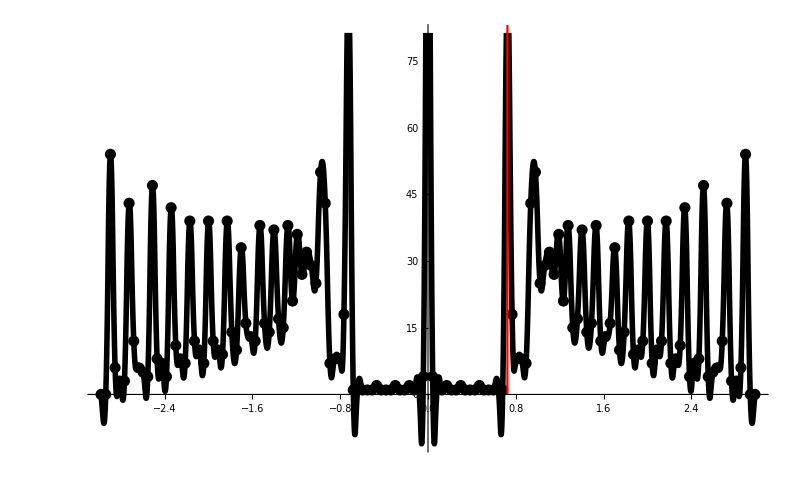

```mathematica
binedges=HistogramList[a0b0d35ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d35ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.85},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{83.9868,{x→0.765929}}

0.765929

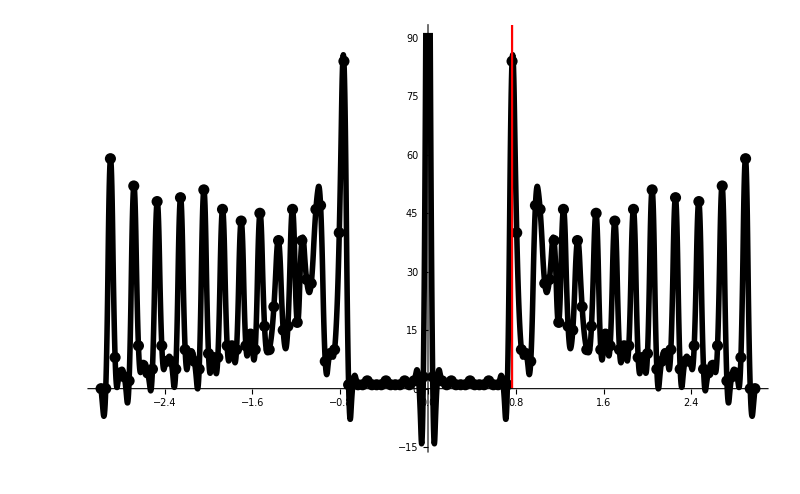

```mathematica
binedges=HistogramList[a0b0d4ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0b0d4ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.95},{x,0.8}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

### a0d2 fits

```mathematica
a0d2e1fits={};
```

```mathematica
bw=(3-(-3))/141;
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{10.9999,{x→0.29787}}

0.29787

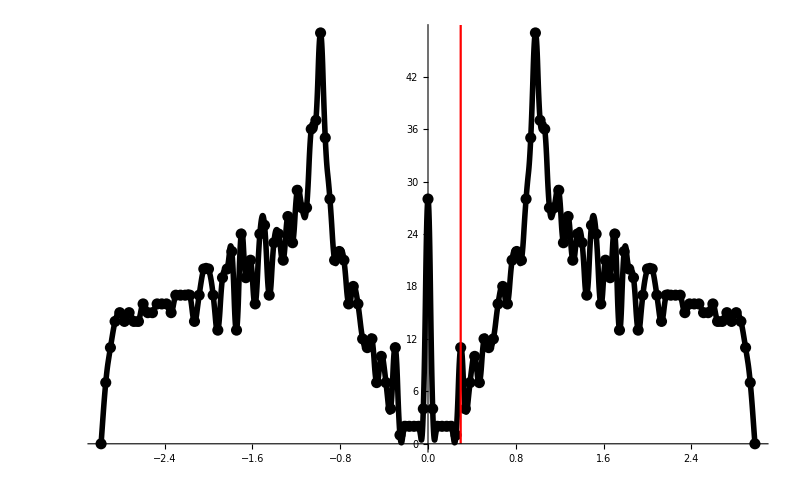

```mathematica
binedges=HistogramList[a0d2b0d05ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d05ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.4},{x,0.3}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{14.9987,{x→0.383035}}

0.383035

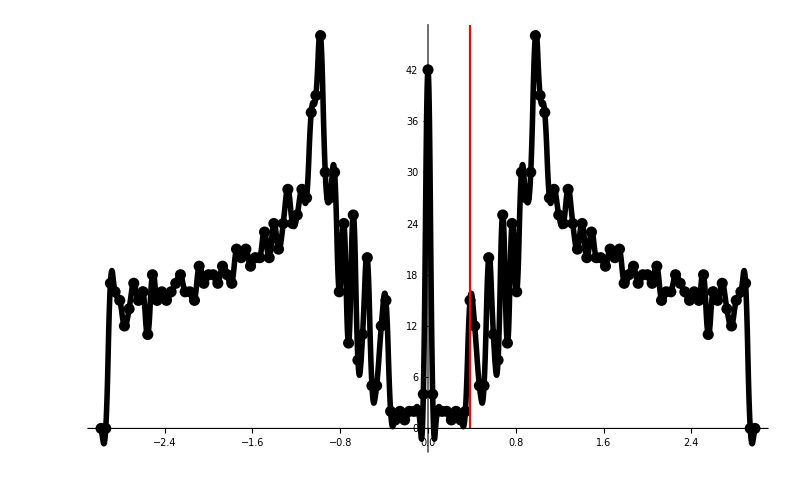

```mathematica
binedges=HistogramList[a0d2b0d1ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d1ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.3≤x≤0.5},{x,0.4}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{25.,{x→0.468085}}

0.468085

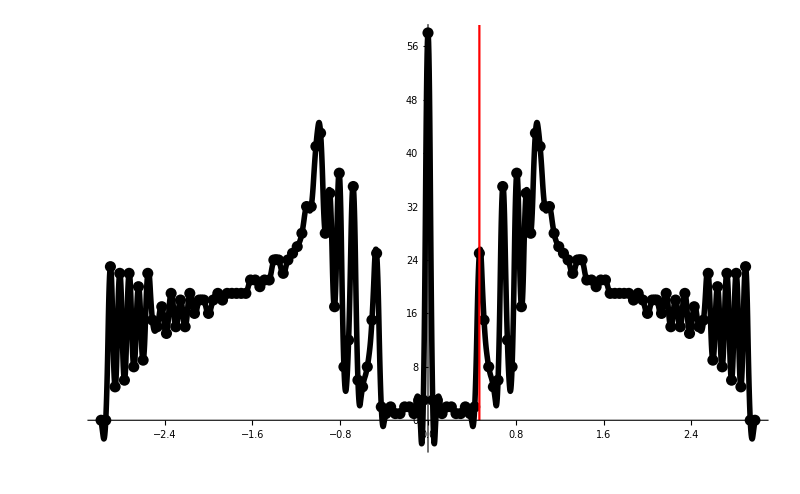

```mathematica
binedges=HistogramList[a0d2b0d15ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d15ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.6},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{48.9996,{x→0.553188}}

0.553188

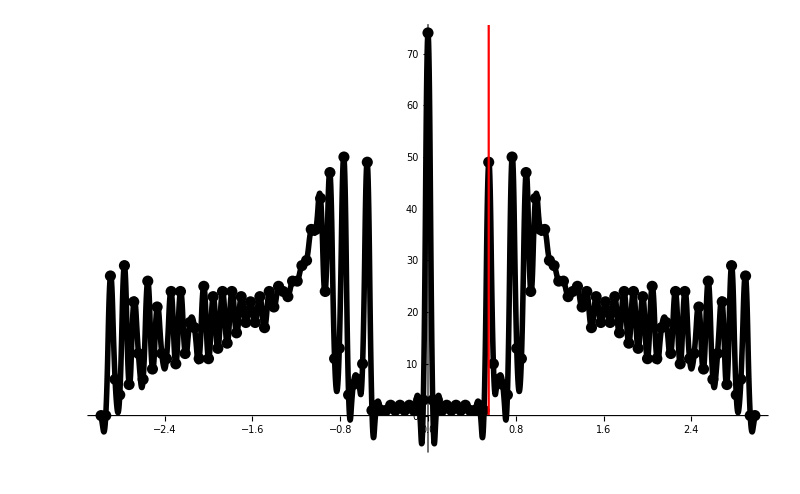

```mathematica
binedges=HistogramList[a0d2b0d2ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d2ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.65},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{70.9997,{x→0.638293}}

0.638293

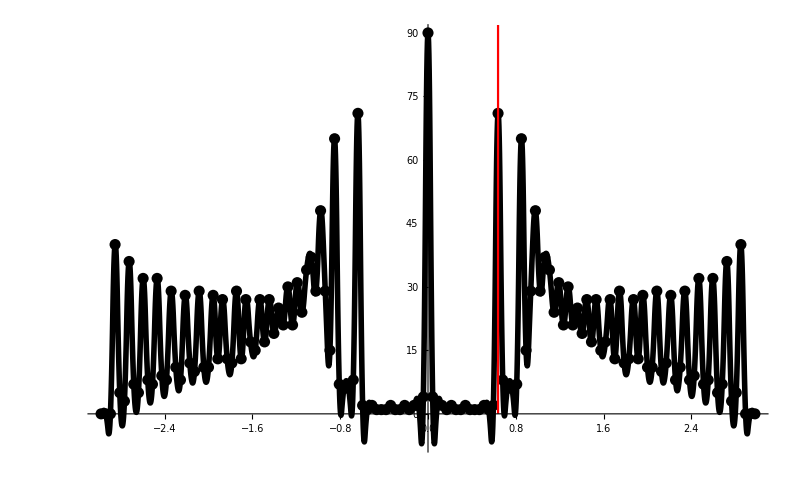

```mathematica
binedges=HistogramList[a0d2b0d25ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d25ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.75},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{83.9898,{x→0.680855}}

0.680855

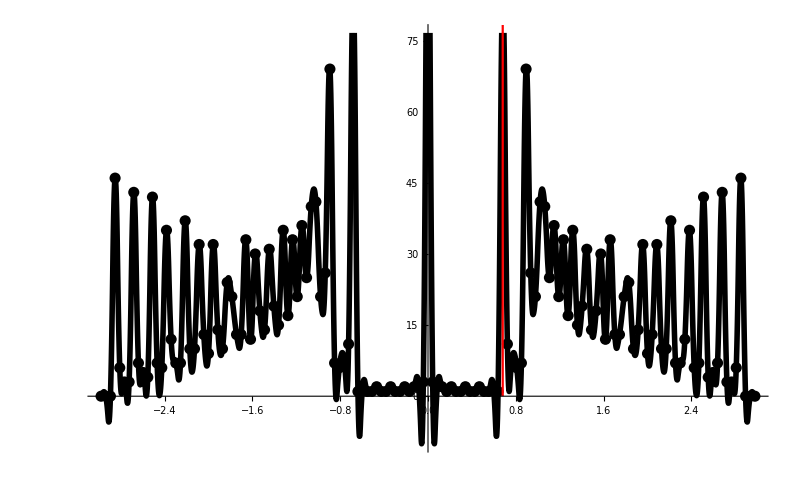

```mathematica
binedges=HistogramList[a0d2b0d3ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d3ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.8},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{98.9999,{x→0.723404}}

0.723404

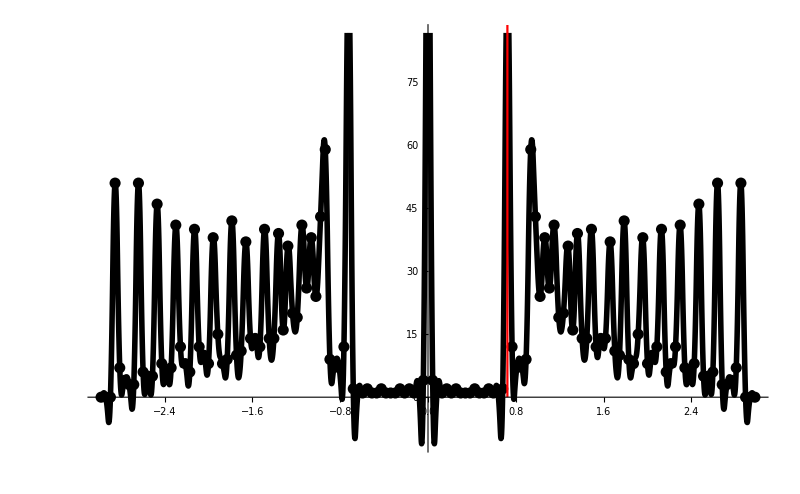

```mathematica
binedges=HistogramList[a0d2b0d35ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d35ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.8},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

{97.0123,{x→0.765432}}

0.765432

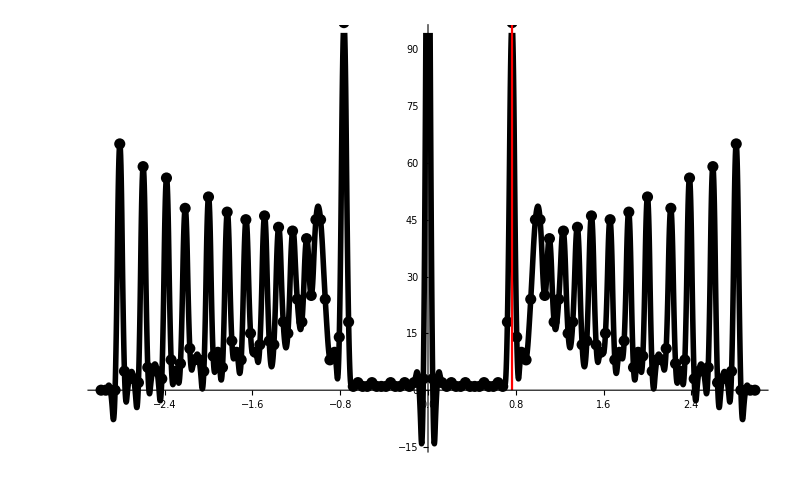

```mathematica
binedges=HistogramList[a0d2b0d4ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d2b0d4ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.9},{x,0.75}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d2e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

### a0d4 fits

```mathematica
a0d4e1fits={};
```

```mathematica
bw=(3-(-3))/141;
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{8.,{x→0.255319}}

0.255319

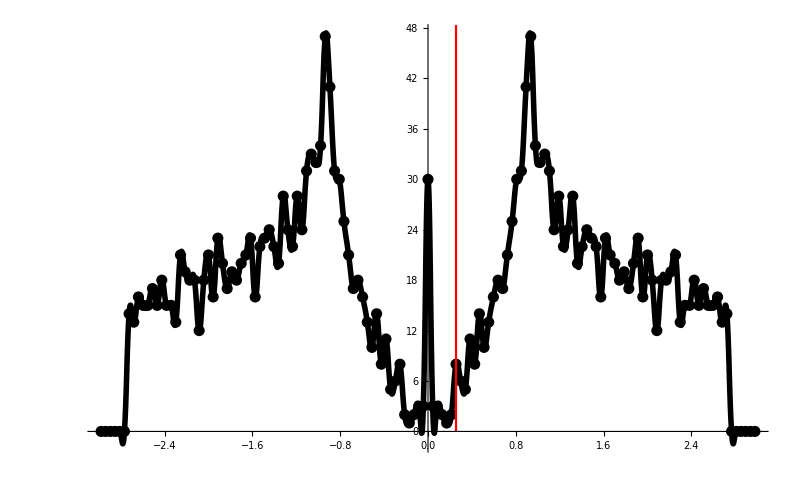

```mathematica
binedges=HistogramList[a0d4b0d05ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d05ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.4},{x,0.3}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{23.9998,{x→0.382977}}

0.382977

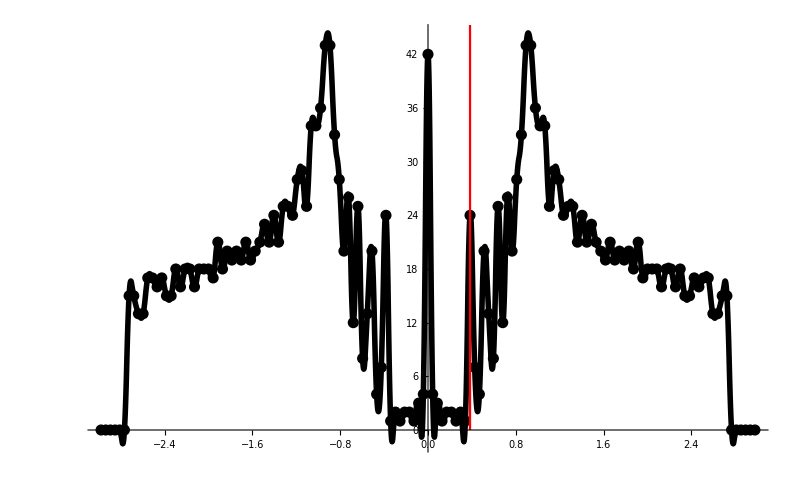

```mathematica
binedges=HistogramList[a0d4b0d1ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d1ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.3≤x≤0.5},{x,0.4}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{38.9994,{x→0.468074}}

0.468074

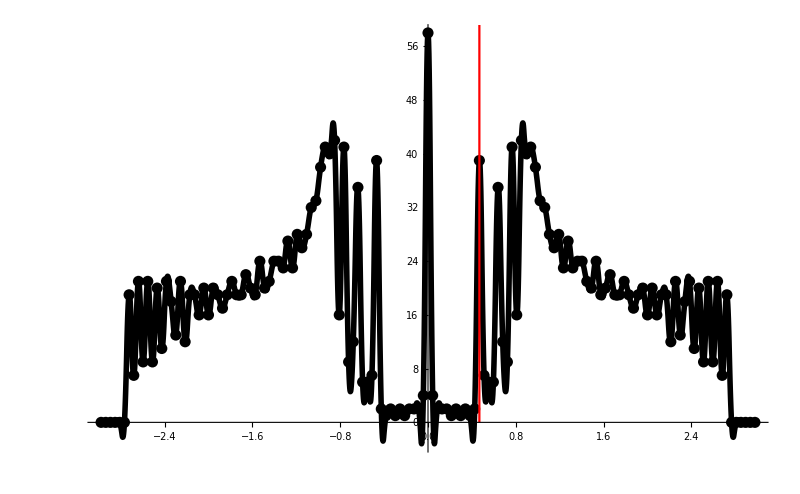

```mathematica
binedges=HistogramList[a0d4b0d15ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d15ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.6},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{45.9996,{x→0.510635}}

0.510635

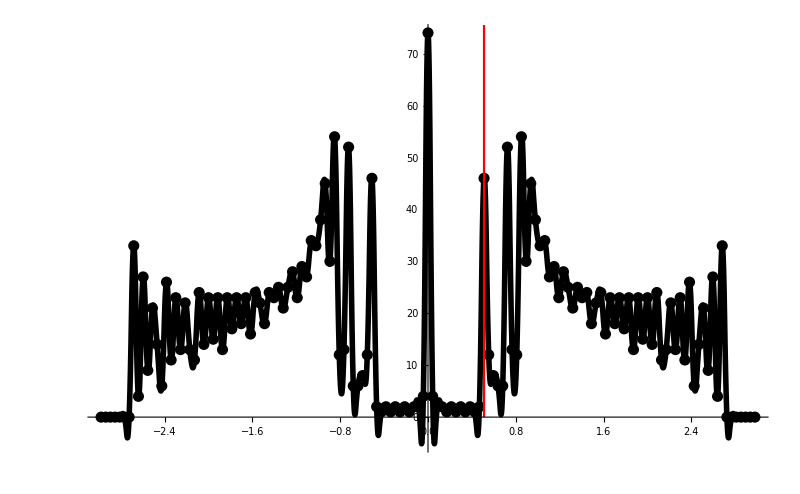

```mathematica
binedges=HistogramList[a0d4b0d2ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d2ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.6},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{70.9996,{x→0.595739}}

0.595739

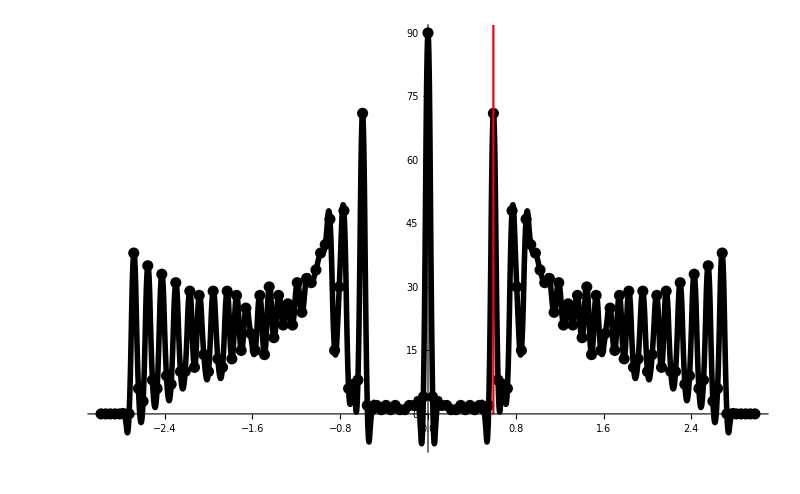

```mathematica
binedges=HistogramList[a0d4b0d25ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d25ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.5≤x≤0.7},{x,0.6}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{85.9981,{x→0.638278}}

0.638278

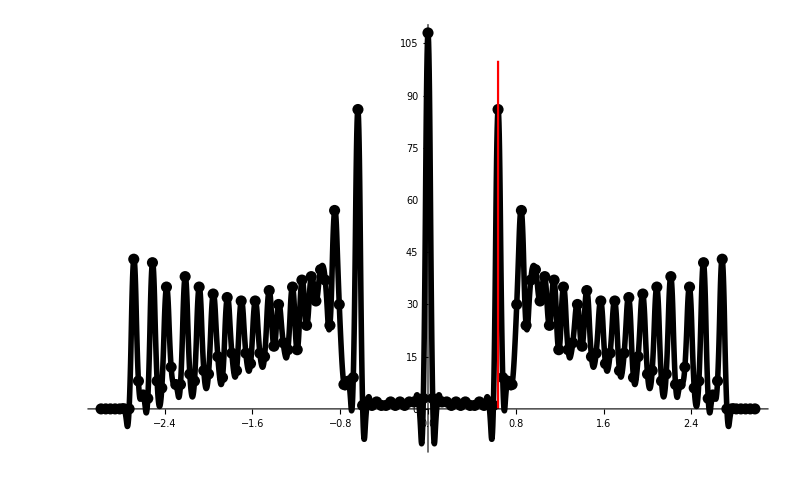

```mathematica
binedges=HistogramList[a0d4b0d3ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d3ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.5≤x≤0.8},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{102.,{x→0.680846}}

0.680846

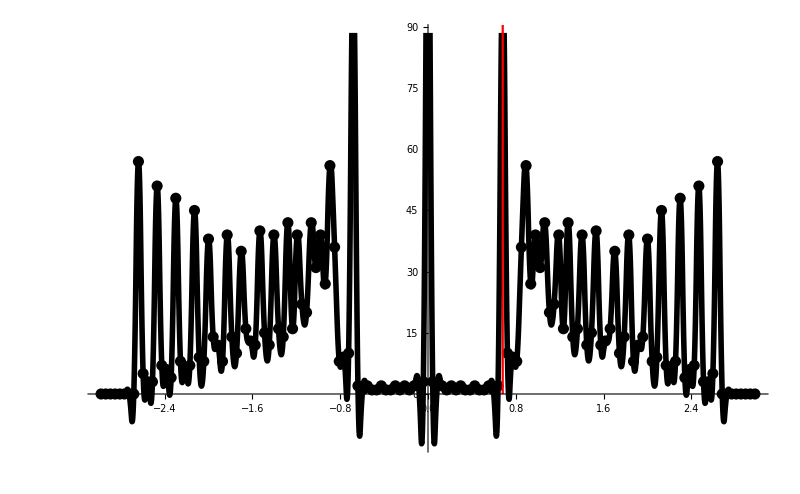

```mathematica
binedges=HistogramList[a0d4b0d35ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d35ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.8},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

{88.3068,{x→0.720503}}

0.720503

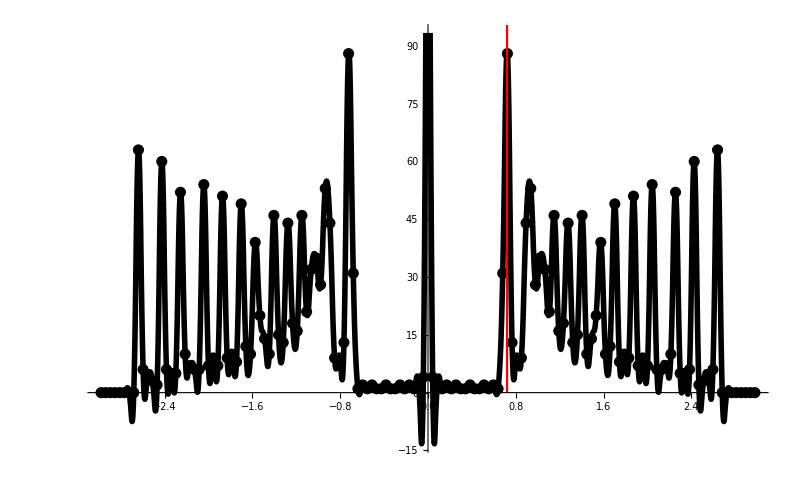

```mathematica
binedges=HistogramList[a0d4b0d4ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d4b0d4ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.6≤x≤0.8},{x,0.7}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d4e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

### a0d6 fits

```mathematica
a0d6e1fits={};
```

```mathematica
bw=(3-(-3))/141;
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{9.99994,{x→0.255314}}

0.255314

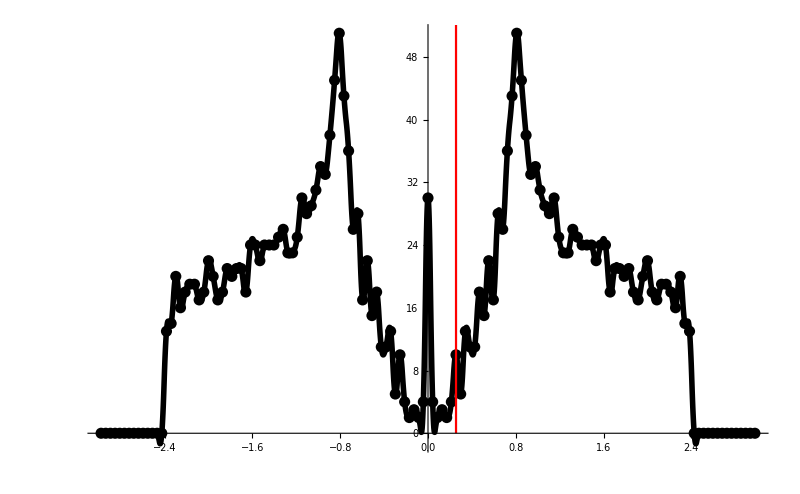

```mathematica
binedges=HistogramList[a0d6b0d05ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d05ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.35},{x,0.22}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{24.9998,{x→0.340421}}

0.340421

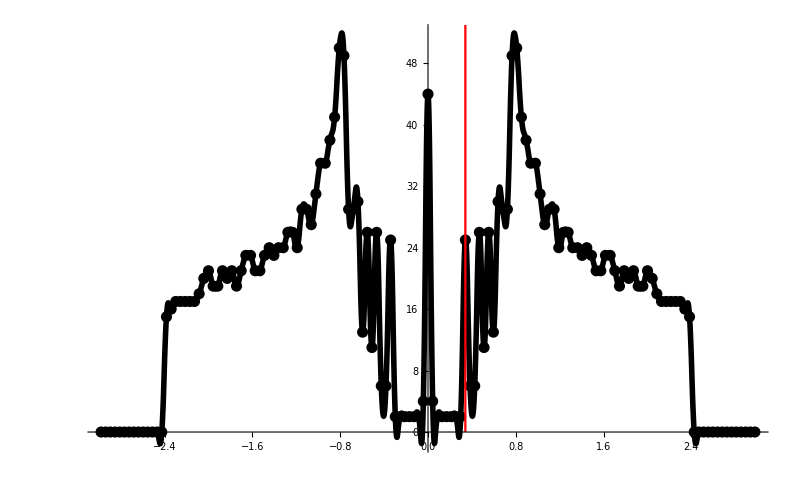

```mathematica
binedges=HistogramList[a0d6b0d1ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d1ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.4},{x,0.3}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{31.9998,{x→0.382977}}

0.382977

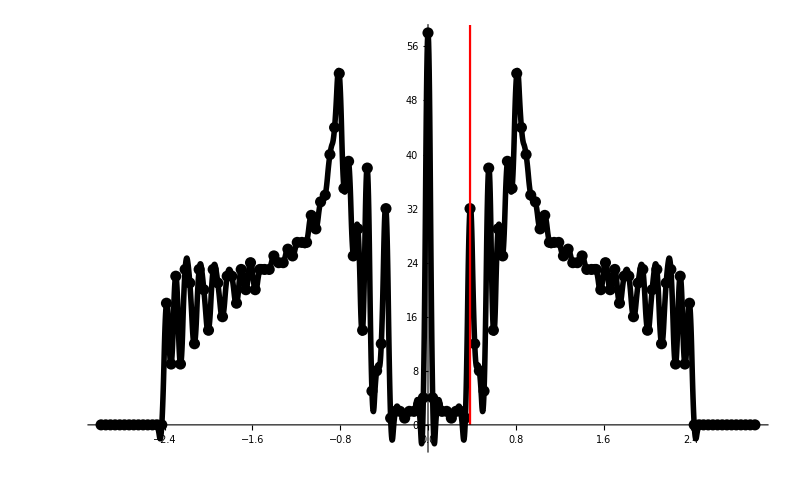

```mathematica
binedges=HistogramList[a0d6b0d15ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d15ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.3≤x≤0.5},{x,0.4}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{54.9978,{x→0.468058}}

0.468058

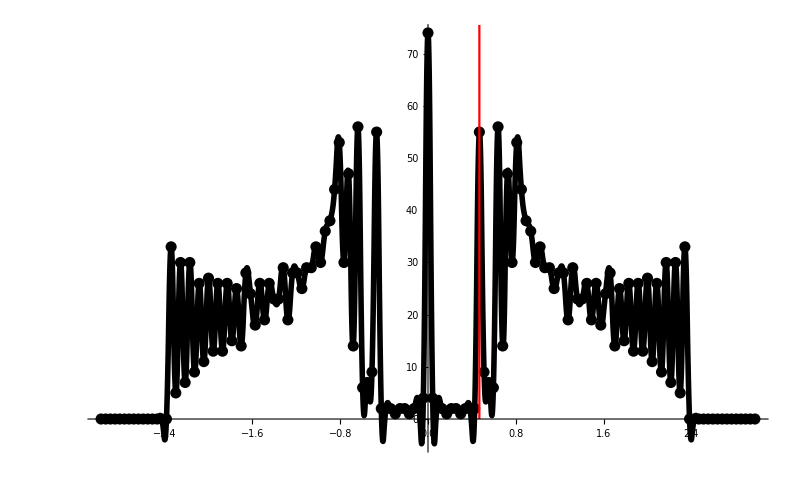

```mathematica
binedges=HistogramList[a0d6b0d2ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d2ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.6},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{69.9996,{x→0.510634}}

0.510634

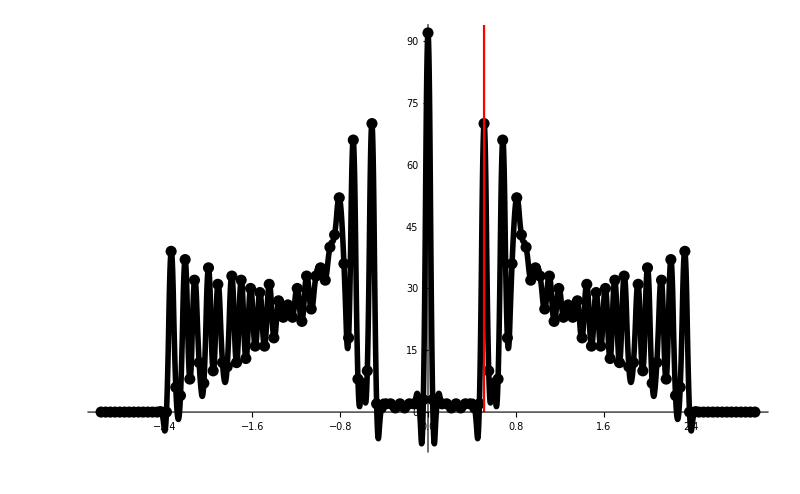

```mathematica
binedges=HistogramList[a0d6b0d25ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d25ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.6},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{84.9999,{x→0.55319}}

0.55319

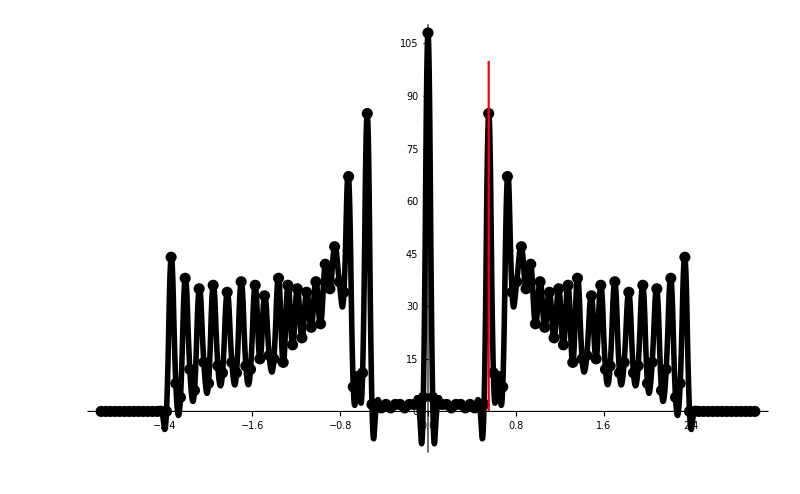

```mathematica
binedges=HistogramList[a0d6b0d3ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d3ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.65},{x,0.5}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{101.999,{x→0.59574}}

0.59574

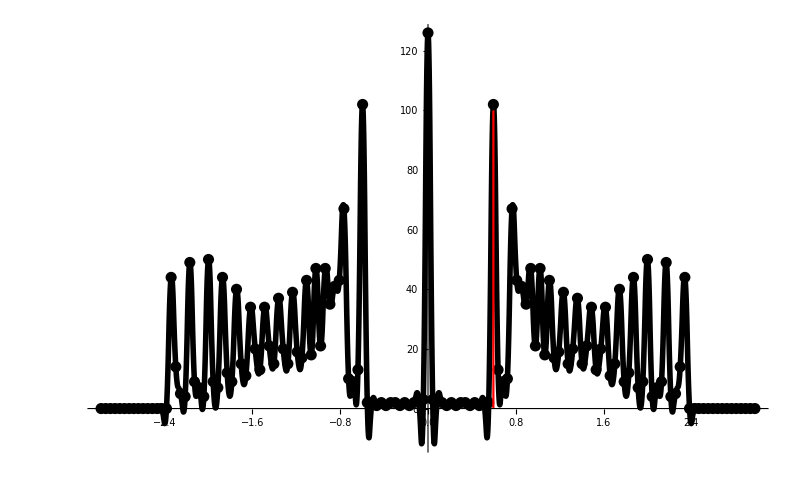

```mathematica
binedges=HistogramList[a0d6b0d35ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d35ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.5≤x≤0.7},{x,0.6}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

{78.4329,{x→0.630907}}

0.630907

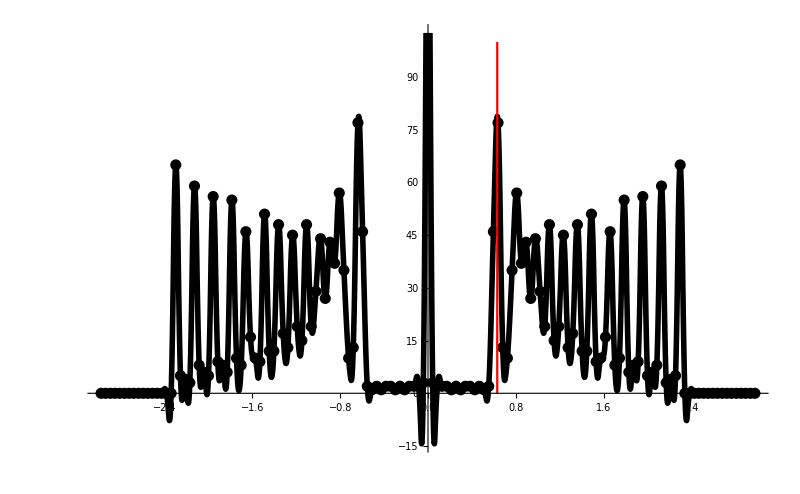

```mathematica
binedges=HistogramList[a0d6b0d4ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d6b0d4ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.5≤x≤0.75},{x,0.6}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d6e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

### a0d8 fits

```mathematica
a0d8e1fits={};
```

```mathematica
bw=(3-(-3))/141;
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{9.99211,{x→0.17028}}

0.17028

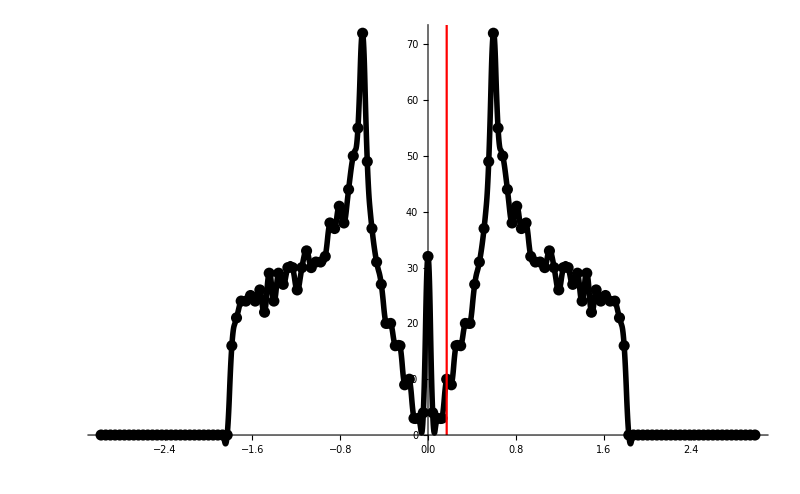

```mathematica
binedges=HistogramList[a0d8b0d05ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d05ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.1≤x≤0.25},{x,0.12}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{26.9983,{x→0.255295}}

0.255295

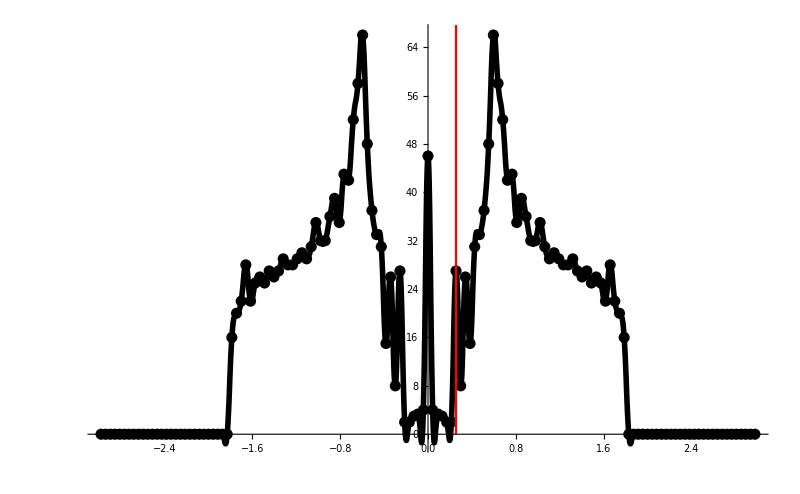

```mathematica
binedges=HistogramList[a0d8b0d1ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d1ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.35},{x,0.22}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{39.9997,{x→0.297868}}

0.297868

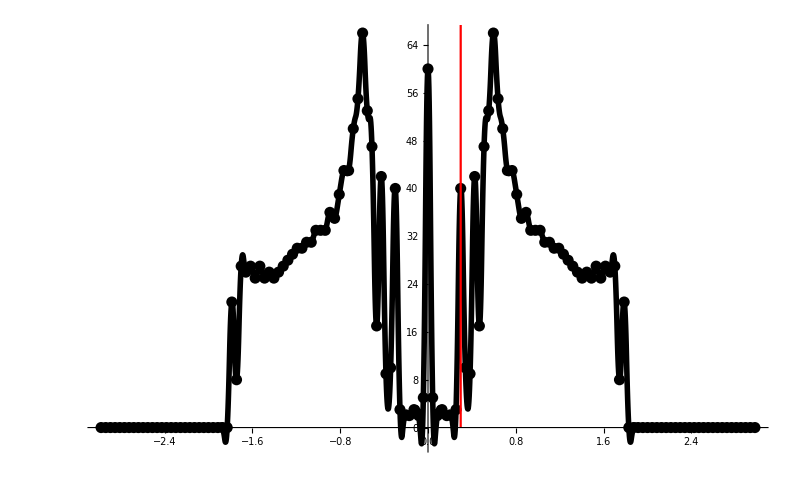

```mathematica
binedges=HistogramList[a0d8b0d15ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d15ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.35},{x,0.25}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{53.9996,{x→0.340422}}

0.340422

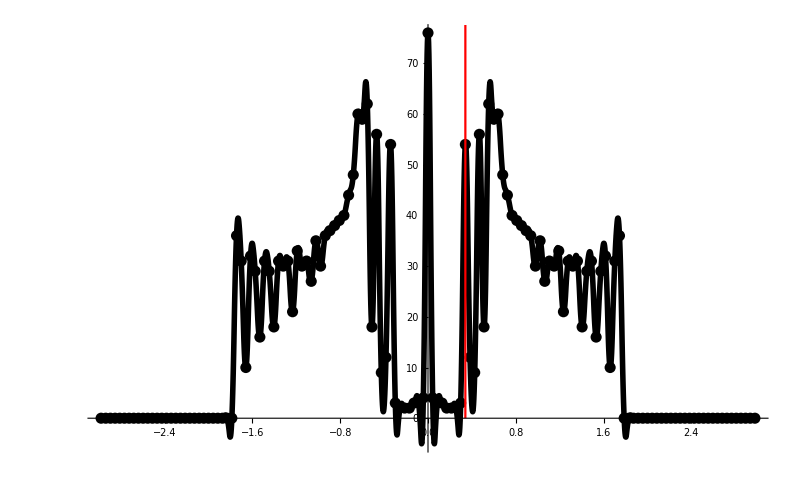

```mathematica
binedges=HistogramList[a0d8b0d2ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d2ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.4},{x,0.3}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{71.9969,{x→0.38295}}

0.38295

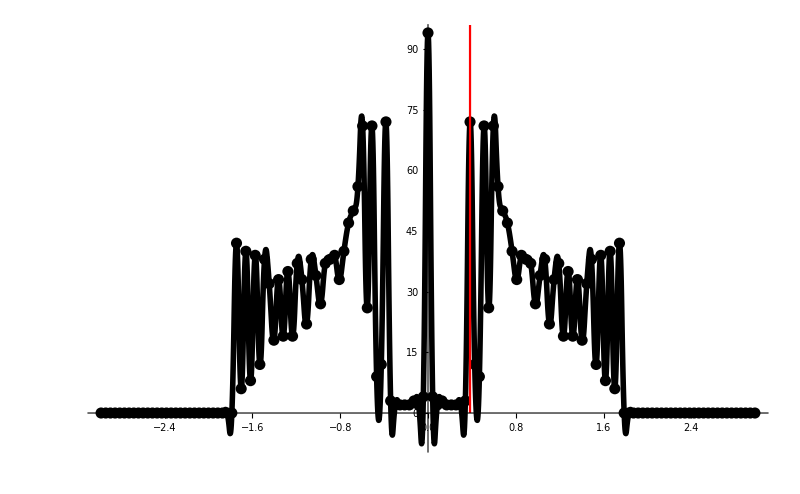

```mathematica
binedges=HistogramList[a0d8b0d25ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d25ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.2≤x≤0.45},{x,0.3}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{90.9967,{x→0.425504}}

0.425504

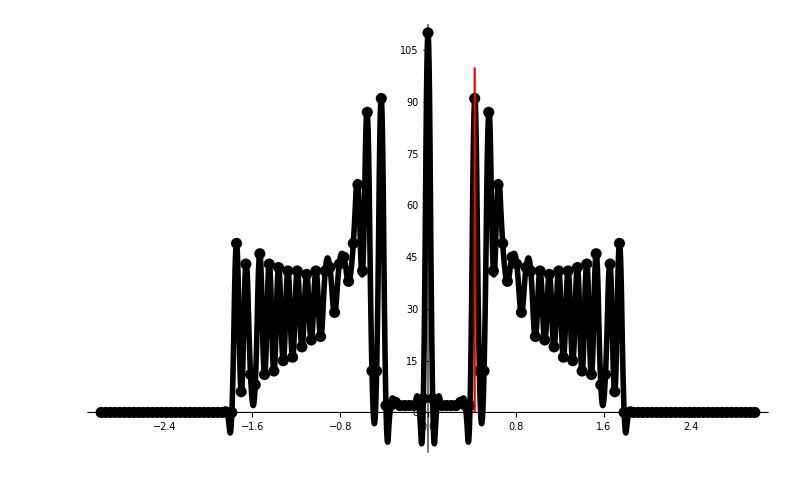

```mathematica
binedges=HistogramList[a0d8b0d3ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d3ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.55},{x,0.45}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{90.9703,{x→0.425545}}

0.425545

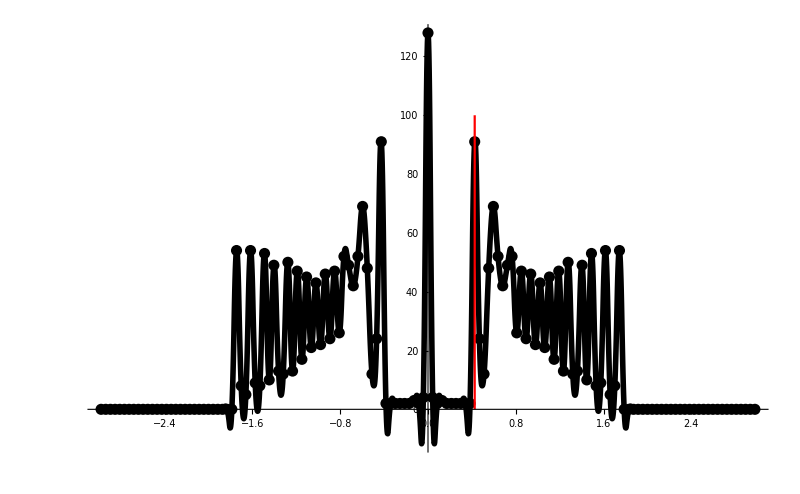

```mathematica
binedges=HistogramList[a0d8b0d35ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d35ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.55},{x,0.45}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{119.999,{x→0.46808}}

0.46808

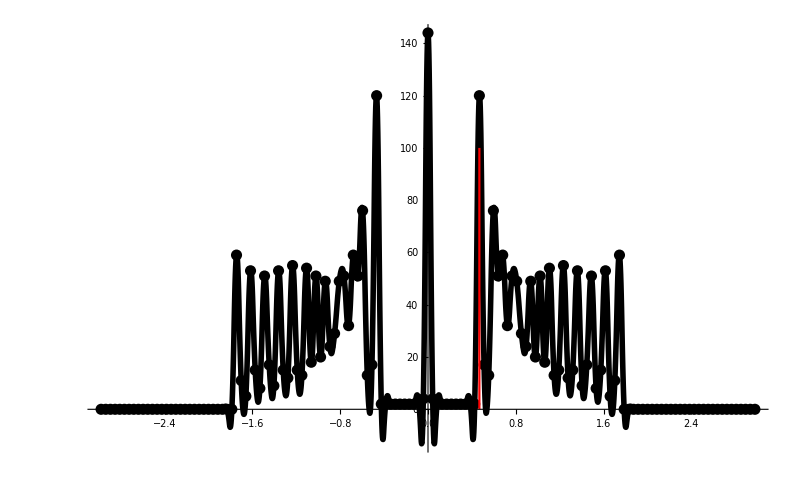

```mathematica
binedges=HistogramList[a0d8b0d4ev,{-3,3,bw}][[1]];(**)
bincenters = binedges[[;;-2]]+(bw/2);
counts = HistogramList[a0d8b0d4ev,{-3,3,bw}][[2]];(**)
fint=Interpolation[Transpose@{bincenters,counts},InterpolationOrder->2];
resmax=FindMaximum[{fint[x],0.4≤x≤0.55},{x,0.45}](**)
resmaxloc=x/.resmax[[2]]
AppendTo[a0d8e1fits,resmaxloc];
Show[
ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Black,Thickness[0.005]}],
ListPlot[Transpose@{bincenters,counts},PlotStyle->{Black,PointSize[0.01]}],
ListPlot[Transpose@{{resmaxloc, resmaxloc},{0,100}},Joined->True,InterpolationOrder->1,PlotStyle->Red],
ImageSize->800
]
```

## Scaling

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
```

```mathematica
betalist={0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4};
```

```mathematica
a0e1=a0e1fits;
a0d2e1=a0d2e1fits;
a0d4e1=a0d4e1fits;
a0d6e1=a0d6e1fits;
a0d8e1=a0d8e1fits;
```

```mathematica
datadir="/home/cal422/PycharmProjects/Hyperbolic_Lattice_Self_Consistent_Hartree_Fock_Data_Acquisition/Mathematica_Final_Plots/Final_Data/NH_withBField_FinalHoneycombScalingData/FirstTenGen";
```

```mathematica
a0vcrit=Import[StringJoin[datadir,"/honeycomb_nl20a0_withBField_nearVCrit_firstTenGen.txt"],"Table"];
a0d2vcrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.2_withBField_nearVCrit_firstTenGen.txt"],"Table"];
a0d4vcrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.4_withBField_nearVCrit_firstTenGen.txt"],"Table"];
a0d6vcrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.6_withBField_nearVCrit_firstTenGen.txt"],"Table"];
a0d8vcrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.8_withBField_nearVCrit_firstTenGen.txt"],"Table"];
```

```mathematica
a0ucrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.0_withBField_nearUCrit_firstTenGen.txt"],"Table"];
a0d2ucrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.2_withBField_nearUCrit_firstTenGen.txt"],"Table"];
a0d4ucrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.4_withBField_nearUCrit_firstTenGen.txt"],"Table"];
a0d6ucrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.6_withBField_nearUCrit_firstTenGen.txt"],"Table"];
a0d8ucrit=Import[StringJoin[datadir,"/honeycomb_nl20a0.8_withBField_nearUCrit_firstTenGen.txt"],"Table"];
```

```mathematica
psize=0.03;
lthickness=0.005;
```

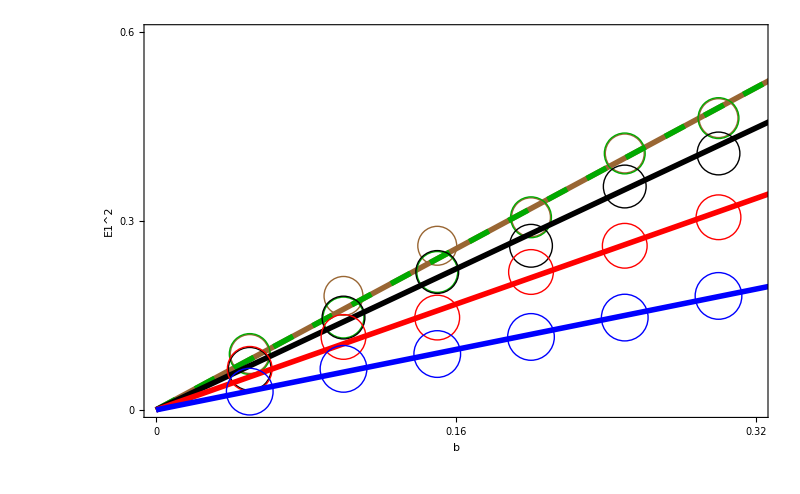

```mathematica
xrange={0,0.32};
yrange={0,0.6};
Show[
ListPlot[Transpose@{betalist,a0e1^2},PlotRange->{xrange,yrange},PlotMarkers->Style[○,40,Brown]],
Plot[1.6*x,{x,0,7},PlotStyle->{Brown,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{betalist,a0d2e1^2}, PlotRange->{xrange,yrange},PlotMarkers->Style[○,42,Darker[Green]]],
Plot[1.6*x,{x,0,7},PlotStyle->{Darker[Green],Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{betalist,a0d4e1^2}, PlotRange->{xrange,yrange},PlotMarkers->Style[○,44,Black]],
Plot[1.4*x,{x,0,7},PlotStyle->{Black,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{betalist,a0d6e1^2}, PlotRange->{xrange,yrange},PlotMarkers->Style[○,46,Red]],
Plot[1.05*x,{x,0,7},PlotStyle->{Red,Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{betalist,a0d8e1^2}, PlotRange->{xrange,yrange},PlotMarkers->Style[○,48,Blue]],
Plot[0.6*x,{x,0,7},PlotStyle->{Blue,Thickness[lthickness]},PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"b","E1^2"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.3,0.6},None},{{0,0.16,0.32},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
e1fitlist={1.6,1.6,1.4,1.05,0.6};
```

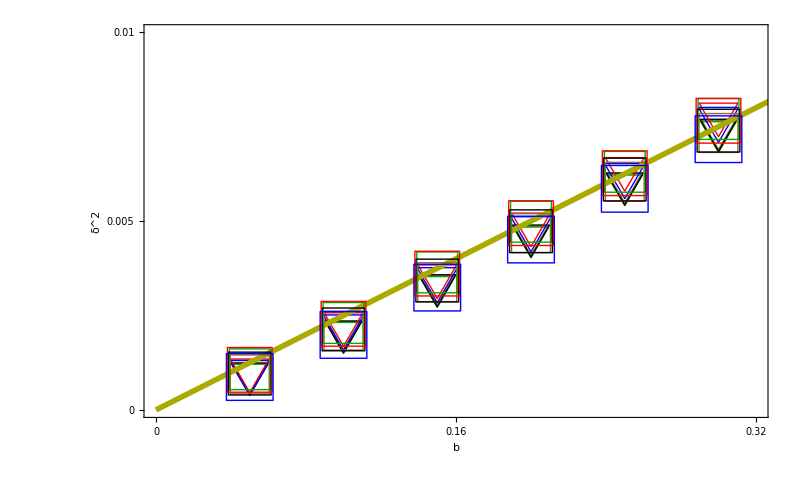

```mathematica
xrange={0,0.32};
yrange={0,0.01};
Show[
ListPlot[Transpose@{a0vcrit[[1]],a0vcrit[[2]]^2},PlotMarkers->Style[▽,40,Brown],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d2vcrit[[1]],a0d2vcrit[[2]]^2},PlotMarkers->Style[▽,42,Darker[Green]],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d4vcrit[[1]],a0d4vcrit[[2]]^2},PlotMarkers->Style[▽,44,Black],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d6vcrit[[1]],a0d6vcrit[[2]]^2},PlotMarkers->Style[▽,46,Red],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d8vcrit[[1]],a0d8vcrit[[2]]^2},PlotMarkers->Style[▽,48,Blue],PlotRange->{xrange,yrange}],
Plot[0.025*x,{x,0,0.7},PlotStyle->{Darker[Yellow],Thickness[lthickness]},PlotRange->{xrange,yrange}],

ListPlot[Transpose@{a0ucrit[[1]],a0ucrit[[2]]^2},PlotMarkers->Style[□,40,Brown],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d2ucrit[[1]],a0d2ucrit[[2]]^2},PlotMarkers->Style[□,42,Darker[Green]],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d4ucrit[[1]],a0d4ucrit[[2]]^2},PlotMarkers->Style[□,44,Black],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d6ucrit[[1]],a0d6ucrit[[2]]^2},PlotMarkers->Style[□,46,Red],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{a0d8ucrit[[1]],a0d8ucrit[[2]]^2},PlotMarkers->Style[□,48,Blue],PlotRange->{xrange,yrange}],
(*Plot[0.0315*x,{x,0,0.7},PlotStyle->{Darker[Yellow],Thickness[lthickness],Dashing[0.02]},PlotRange->{xrange,yrange}],*)

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"b","δ^2"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.005,0.01},None},{{0,0.16,0.32},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
cvals=Sqrt[e1fitlist/0.025]
alphas={0,0.2,0.4,0.6,0.8};
```

{8.,8.,7.48331,6.48074,4.89898}

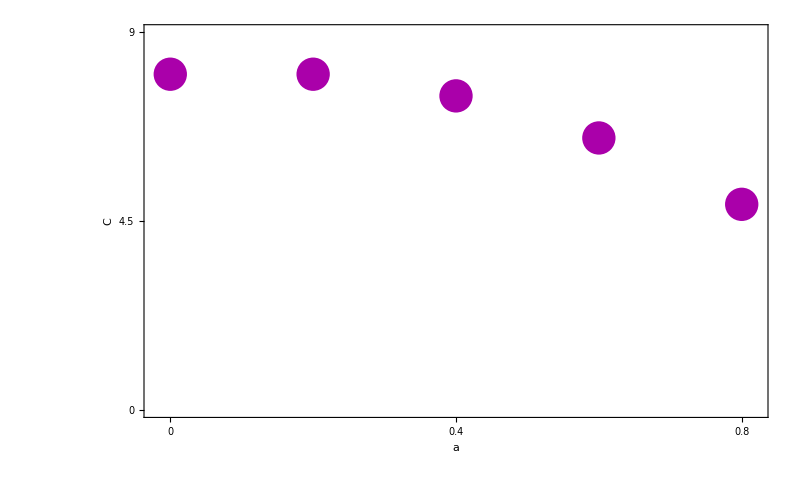

```mathematica
xrange={-0.02,0.82};
yrange={0,9};
Show[
ListPlot[Transpose@{alphas, cvals},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"a","C"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,4.5,9},None},{{0,0.4,0.8},None}},FrameTicksStyle->FontSize->50
]
```

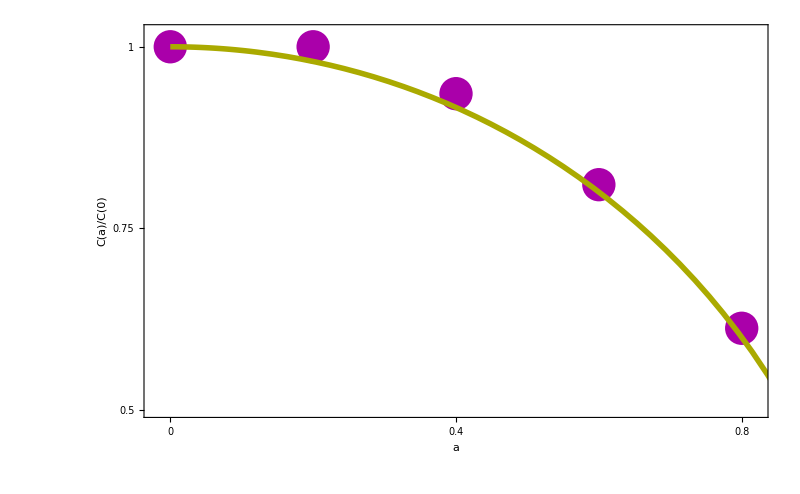

```mathematica
cvalsratio=cvals/cvals[[1]];
xrange={-0.02,0.82};
yrange={0.5,1.02};
Show[
ListPlot[Transpose@{alphas, cvalsratio},PlotStyle->{Darker[Magenta],PointSize[psize]},PlotRange->{xrange,yrange}],
Plot[(1-x^2)^(1/2),{x,0,1},PlotStyle->{Darker[Yellow],Thickness[lthickness]},PlotRange->{xrange,yrange}],

BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"a","C(a)/C(0)"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0.5,0.75,1},None},{{0,0.4,0.8},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
a0vcritsort=a0vcrit[[2]][[Ordering[a0vcrit[[1]]]]];
a0d2vcritsort=a0d2vcrit[[2]][[Ordering[a0d2vcrit[[1]]]]];
a0d4vcritsort=a0d4vcrit[[2]][[Ordering[a0d4vcrit[[1]]]]];
a0d6vcritsort=a0d6vcrit[[2]][[Ordering[a0d6vcrit[[1]]]]];
a0d8vcritsort=a0d8vcrit[[2]][[Ordering[a0d8vcrit[[1]]]]];
```

```mathematica
a0coulombcval=Mean[((a0e1^2)/(a0vcritsort[[;;8]]^2))[[;;6]]];
a0d2coulombcval=Mean[((a0d2e1^2)/(a0d2vcritsort[[;;8]]^2))[[;;6]]];
a0d4coulombcval=Mean[((a0d4e1^2)/(a0d4vcritsort[[;;8]]^2))[[;;6]]];
a0d6coulombcval=Mean[((a0d6e1^2)/(a0d6vcritsort[[;;8]]^2))[[;;6]]];
a0d8coulombcval=Mean[((a0d8e1^2)/(a0d8vcritsort[[;;8]]^2))[[;;6]]];
```

```mathematica
a0ucritsort=a0ucrit[[2]][[Ordering[a0ucrit[[1]]]]];
a0d2ucritsort=a0d2ucrit[[2]][[Ordering[a0d2ucrit[[1]]]]];
a0d4ucritsort=a0d4ucrit[[2]][[Ordering[a0d4ucrit[[1]]]]];
a0d6ucritsort=a0d6ucrit[[2]][[Ordering[a0d6ucrit[[1]]]]];
a0d8ucritsort=a0d8ucrit[[2]][[Ordering[a0d8ucrit[[1]]]]];
```

```mathematica
a0hubbardcval=Mean[((a0e1^2)/(a0ucritsort[[;;8]]^2))[[;;6]]];
a0d2hubbardcval=Mean[((a0d2e1^2)/(a0d2ucritsort[[;;8]]^2))[[;;6]]];
a0d4hubbardcval=Mean[((a0d4e1^2)/(a0d4ucritsort[[;;8]]^2))[[;;6]]];
a0d6hubbardcval=Mean[((a0d6e1^2)/(a0d6ucritsort[[;;8]]^2))[[;;6]]];
a0d8hubbardcval=Mean[((a0d8e1^2)/(a0d8ucritsort[[;;8]]^2))[[;;6]]];
```

```mathematica
cvalscoulomb=Sqrt[{a0coulombcval,a0d2coulombcval,a0d4coulombcval,a0d6coulombcval,a0d8coulombcval}];
cvalshubbard=Sqrt[{a0hubbardcval,a0d2hubbardcval,a0d4hubbardcval,a0d6hubbardcval,a0d8hubbardcval}];
```

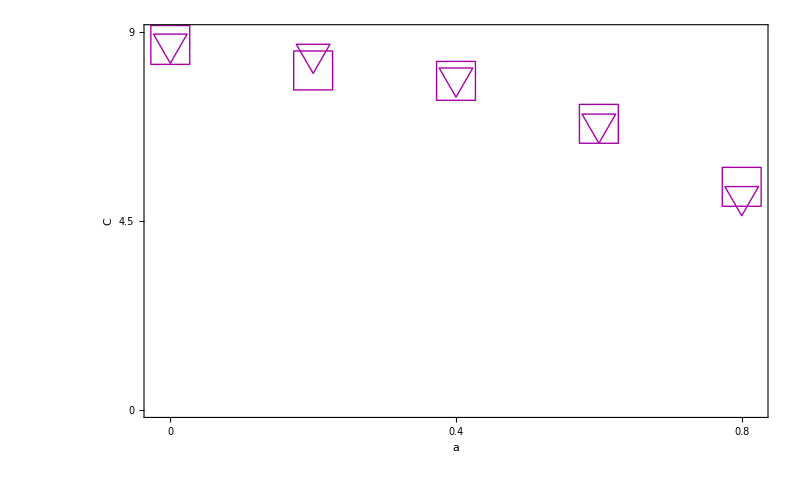

```mathematica
xrange={-0.02,0.82};
yrange={0,9};
Show[
ListPlot[Transpose@{alphas, cvalscoulomb},PlotMarkers->Style[▽,40,Darker[Magenta]],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{alphas, cvalshubbard},PlotMarkers->Style[□,40,Darker[Magenta]],PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"a","C"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,4.5,9},None},{{0,0.4,0.8},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
cvalscoulombratio=cvalscoulomb/cvalscoulomb[[1]];
cvalshubbardratio=cvalshubbard/cvalshubbard[[1]];
```

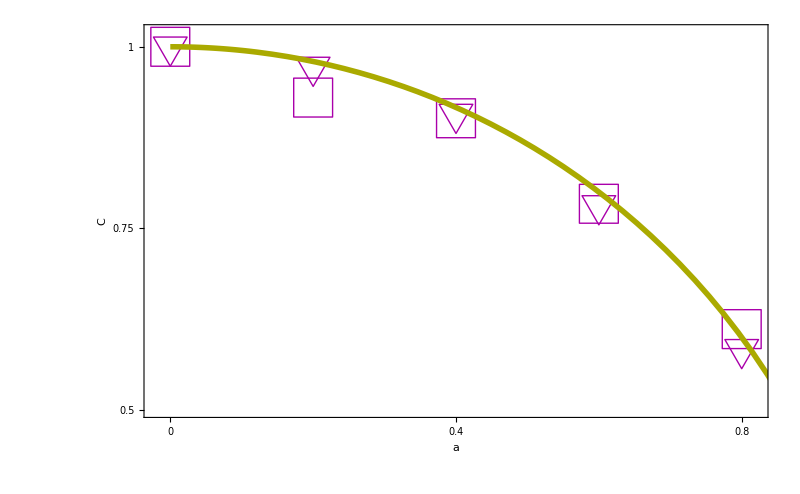

```mathematica
xrange={-0.02,0.82};
yrange={0.5,1.02};
Show[
ListPlot[Transpose@{alphas, cvalscoulombratio},PlotMarkers->Style[▽,40,Darker[Magenta]],PlotRange->{xrange,yrange}],
ListPlot[Transpose@{alphas, cvalshubbardratio},PlotMarkers->Style[□,40,Darker[Magenta]],PlotRange->{xrange,yrange}],
Plot[(1-x^2)^(1/2),{x,0,1},PlotStyle->{Darker[Yellow],Thickness[lthickness]},PlotRange->{xrange,yrange}],


BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"a","C"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0.5,0.75,1},None},{{0,0.4,0.8},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
Sort[a0vcrit[[1]]][[;;6]]
Sort[a0d2vcrit[[1]]][[;;6]]
Sort[a0d4vcrit[[1]]][[;;6]]
Sort[a0d6vcrit[[1]]][[;;6]]
Sort[a0d8vcrit[[1]]][[;;6]]
```

{0.0500000000000000028,0.100000000000000006,0.149999999999999994,0.200000000000000011,0.25,0.299999999999999989}

{0.0500000000000000028,0.100000000000000006,0.149999999999999994,0.200000000000000011,0.25,0.299999999999999989}

{0.0500000000000000028,0.100000000000000006,0.149999999999999994,0.200000000000000011,0.25,0.299999999999999989}

«2 more identical outputs»

```mathematica
Sort[a0ucrit[[1]]][[;;6]]
Sort[a0d2ucrit[[1]]][[;;6]]
Sort[a0d4ucrit[[1]]][[;;6]]
Sort[a0d6ucrit[[1]]][[;;6]]
Sort[a0d8ucrit[[1]]][[;;6]]
```

{0.0500000000000000028,0.100000000000000006,0.149999999999999994,0.200000000000000011,0.25,0.299999999999999989}

{0.0500000000000000028,0.100000000000000006,0.149999999999999994,0.200000000000000011,0.25,0.299999999999999989}

{0.0500000000000000028,0.100000000000000006,0.149999999999999994,0.200000000000000011,0.25,0.299999999999999989}

«2 more identical outputs»

```mathematica
betalist[[;;6]]
```

{0.05,0.1,0.15,0.2,0.25,0.3}